```mathematica
Lab 6
Variant 5
```

N=4. M=10.

Сетка ω: 0.1
0.005 | 0.2
0.005 | 0.3
0.005 | 0.4
0.005 | 0.5
0.005 | 0.6
0.005 | 0.7
0.005 | 0.8
0.005 | 0.9
0.005 | 1.
0.005
0.1
0.01 | 0.2
0.01 | 0.3
0.01 | 0.4
0.01 | 0.5
0.01 | 0.6
0.01 | 0.7
0.01 | 0.8
0.01 | 0.9
0.01 | 1.
0.01
0.1
0.015 | 0.2
0.015 | 0.3
0.015 | 0.4
0.015 | 0.5
0.015 | 0.6
0.015 | 0.7
0.015 | 0.8
0.015 | 0.9
0.015 | 1.
0.015
0.1
0.02 | 0.2
0.02 | 0.3
0.02 | 0.4
0.02 | 0.5
0.02 | 0.6
0.02 | 0.7
0.02 | 0.8
0.02 | 0.9
0.02 | 1.
0.02

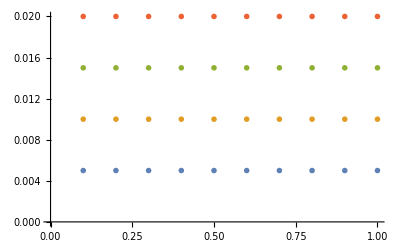

После заполнения границ: 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.025
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0375
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.05

После основного этапа: 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0004375 | 0.0010625 | 0.0019375 | 0.0030625 | 0.0044375 | 0.0060625 | 0.0079375 | 0.0100625 | 0.025
0 | 0.00090625 | 0.0021875 | 0.0039375 | 0.0061875 | 0.0089375 | 0.0121875 | 0.0159375 | 0.0264688 | 0.0375
0 | 0.00140625 | 0.00335938 | 0.006 | 0.009375 | 0.0135 | 0.018375 | 0.0271406 | 0.0366563 | 0.05

```mathematica
(* Начальные условия *)
k=5;
α=0.5*k;
(*D[u[x,t], t]:=D[u[x,t], x,x]+α*(x^2-t);*)
h=0.1;
τ=0.005;
(* Использую NN, так как на N жалуется *)
NN=0.02/τ;
M=1/h;
Print["N=", NN, " M=", M];


(* Задаём сетку *)
ω=Table[0,{i,1,NN}, {j,1,M}];

t= 0;
For[n=1,t=n*τ;t≤ 0.02,n++,
x=0;
For[ m=1, x=m*h; x≤ 1 , m++,
ω⟦n, m⟧ =  {x,t};
]
]
Print["Сетка ω: ",  ω//TableForm];
W = ListPlot[ω,PlotStyle-> PointSize[0.01]]; 
Show[W]

(* Заполняем границы *)
u=Table[0,{i,1,NN}, {j,1,M}];
For[j=1; i=1, j≤ NN, j++,
u⟦j, i⟧ = 0;
]
For[j=1; i=M, j≤ NN, j++,
t=ω⟦j,i, 2⟧;
u⟦j, i⟧ = α*t;
]
For[j=1; i=1, i≤ M, i++,
u⟦j, i⟧ = 0;
]
Print["После заполнения границ: ",  u//TableForm];

(* Основной этап *)
(* В нашем случае a := 1 *)
s= τ/h^2*1;
ϕ[x_,t_]:=α*(x^2-t);
For[n=1, n < NN, n++,
For[m=2, m< M, m++,
x=ω⟦n,m, 1⟧;
t=ω⟦n,m, 2⟧;
u⟦n+1,m⟧=s*u⟦n,m+1⟧+(1-2*s)*u⟦n,m⟧+s*u⟦n,m-1⟧+τ*ϕ[x,t];
]
]
Print["После основного этапа: ",  u//TableForm];
```

```mathematica
(* Проверка (по желанию) *)
Res1={};
For[n=1, n≤ NN, n++,
For[m=1, m<M, m++,
AppendTo[Res1, {ω⟦n,m, 1⟧, ω⟦n,m, 2⟧, u⟦n,m⟧}];
]
]
ListPlot3D[Res1]
```

-Graphics3D-

```mathematica
(* x=a, t=b, u=f *)
Res2 = NDSolve[{D[f[a,b],b]==D[f[a,b],a,a]+α*(a^2-b),f[a,0]==0,f[0,b]==0,f[1,b]==0},f,{b,0,0.02},{a,0,1}];
Plot3D[Evaluate[f[a,b]/.%],{a,0,1},{b,0,0.02}, PlotRange->All]
```

-Graphics3D-